```mathematica
ClearAll["Global`*"]
NotebookSave[]
```

```mathematica
Num=1000;
```

```mathematica
MatA=Import["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Matrices\\MatA.m"];
MatB=Import["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Matrices\\MatB.m"];
fA=Import["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Matrices\\fA.m"];
fB=Import["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Matrices\\fB.m"];
fVA=Import["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Matrices\\fVA.m"];
Param=Import["C:\\Users\\Miguel Ribeiro\\Documents\\GitHub\\Thesis\\Matrices\\Param.m"];
```

```mathematica
MatRand1=Drop[MatA,{},{1,5}];
MatRand2=Drop[MatB,{},{1,5}];
```

```mathematica
For[x=1;Var2={},x≤Dimensions[fVA][[1]],x++,tmp=1/Num*Sum[fA[[w]]*(fVA[[x,w]]-fB[[w]]),{w,1,Num}];AppendTo[Var2,tmp]]
```

```mathematica
Var2/Total[Var2,2]
```

{0.0388234,0.847083,0.114093}

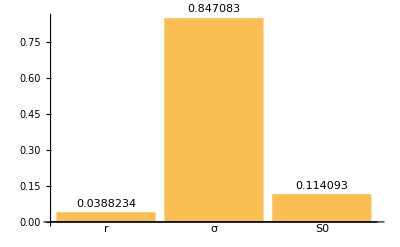

```mathematica
BarChart[Var2/Total[Var2,2],ChartLabels->{"r","σ","S0"},LabelingFunction->Above]
```

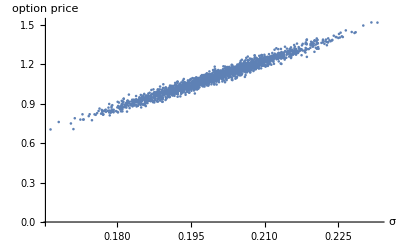

```mathematica
ListPlot[Transpose[Join[{Join[MatRand1[[All,2]],MatRand2[[All,2]]]},{Join[fA,fB]},1]],AxesLabel->{"σ","option price"}]
```

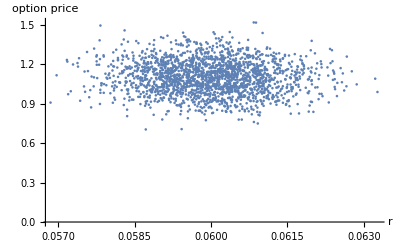

```mathematica
ListPlot[Transpose[Join[{Join[MatRand1[[All,1]],MatRand2[[All,1]]]},{Join[fA,fB]},1]],AxesLabel->{"r","option price"}]
```

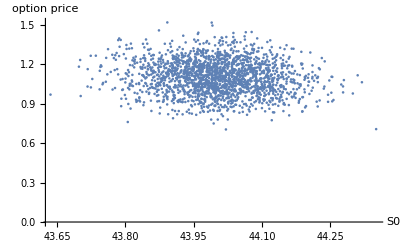

```mathematica
ListPlot[Transpose[Join[{Join[MatRand1[[All,3]],MatRand2[[All,3]]]},{Join[fA,fB]},1]],AxesLabel->{"S0","option price"}]
```

```mathematica
NotebookSave[]
```